```mathematica
f[x_,l_]=Exp[-x^2/(2*l^2)]
```

ⅇ^(-x^2/(2 l^2))

```mathematica
df[x_,l_]=D[f[x,l],x]
```

-(ⅇ^(-x^2/(2 l^2)) x)/l^2

```mathematica
ddf[x_,l_]=D[df[x,l],x]
```

-(ⅇ^(-x^2/(2 l^2)))/l^2+(ⅇ^(-x^2/(2 l^2)) x^2)/l^4

```mathematica
ddf[0,0.4]
```

-6.25

```mathematica
lo=0.4;
```

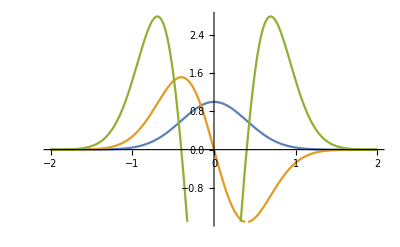

```mathematica
Plot[{f[x,l]/.l->lo,df[x,l]/.l->lo,ddf[x,l]/.l->lo},{x,-2,2}]
```